Biological Modelling and Model Analysis - day IV

Sensitivity and bifurcation analysis

Sander van Doorn

Groningen Institute for Evolutionary Life Sciences

g.s.van.doorn@rug.nl

## Ex. IV-1 Bifurcations in a metapopulation model

The model equations:

```mathematica
eqp=D[p[t],t]==Subscript[c, 1] p[t](1-p[t])-e p[t];
eqq=D[q[t],t]==Subscript[c, 2] q[t](1-p[t]-q[t])-Subscript[c, 1] p[t]q[t]-e q[t];
```

The fixed parameters are:

```mathematica
pars={Subscript[c, 1]->0.3,Subscript[c, 2]->2.};
```

Q(a,b,c): Draw two bifurcation diagrams summarising how the equilibrium frequencies p^* and q^* change as a function of e. How many qualitatively different parameter regimes are there? Identify the types of the bifurcations that occur in this model.

First solve for the equilibria

```mathematica
eql=Solve[{eqp[[2]]==0,eqq[[2]]==0},{p[t],q[t]}]//Simplify
```

{{p[t]→0,q[t]→1-e/c_2},{p[t]→1-e/c_1,q[t]→e/c_1-c_1/c_2},{p[t]→1-e/c_1,q[t]→0},{p[t]→0,q[t]→0}}

One way to find bifurcations is to look at the eigenvalues of the Jacobian at the different equilibrium points

```mathematica
J=D[{eqp[[2]], eqq[[2]]},{{p[t],q[t]}}]
```

{{-e+(1-p[t]) c_1-p[t] c_1,0},{-q[t] c_1-q[t] c_2,-e-p[t] c_1+(1-p[t]-q[t]) c_2-q[t] c_2}}

```mathematica
Subscript[Λ, 1]=Eigenvalues[J/.eql[[1]]]//Simplify
```

{-e+c_1,e-c_2}

```mathematica
Subscript[Λ, 2]=Eigenvalues[J/.eql[[2]]]//Simplify
```

{e-c_1,c_1-(e c_2)/c_1}

```mathematica
Subscript[Λ, 3]=Eigenvalues[J/.eql[[3]]]//Simplify
```

{e-c_1,-c_1+(e c_2)/c_1}

```mathematica
Subscript[Λ, 4]=Eigenvalues[J/.eql[[4]]]//Simplify
```

{-e+c_1,-e+c_2}

From these results, we can see that there are three values of e at which stability changes qualitatively. These separate parameter space into four qualitatively different regimes.

```mathematica
bif1 = Solve[Subscript[Λ, 2][[2]]==0,e]//First
E1=e/.bif1/.pars
```

{e→c_1^2/c_2}

0.045

```mathematica
bif2 = Solve[Subscript[Λ, 1][[1]]==0,e]//First
E2=e/.bif2/.pars
```

{e→c_1}

0.3

```mathematica
bif3 = Solve[Subscript[Λ, 1][[2]]==0,e]//First
E3=e/.bif3/.pars
```

{e→c_2}

2.

Note that at each of these points, there are always two equilibria that undergo a change in stability: for one the dynamics along one of the eigenvectors changes from stable to unstable, for the other, the change occurs in the opposite direction. There is no change in the number of equilibria, suggesting that the bifurcations must all three be transcritical bifurcations. To confirm this idea, we can plot the equilibrium values of the two variables in different styles to visualise how equilibria shift relative to one another. To help interpret this diagram, the location of the bifurcation points is indicated with dotted black lines on the background

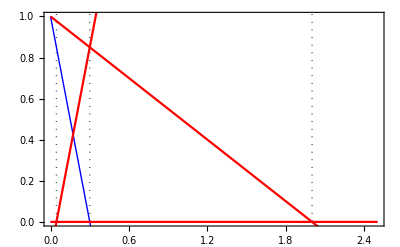

```mathematica
pl1=Plot[{p[t]/.eql[[1]],p[t]/.eql[[2]] }/.pars,{e,0,2.5},PlotStyle->{Thick,Blue}];
pl2=Plot[{q[t]/.eql[[1]],q[t]/.eql[[2]] ,q[t]/.eql[[3]] }/.pars,{e,0,2.5},PlotStyle->{Red}];
Show[{pl1,pl2},Frame->True,PlotRange->{0,1}, Prolog->{Dotted,
Line[{{E1,1.1},{E1,-0.1}}],
Line[{{E2,1.1},{E2,-0.1}}],
Line[{{E3,1.1},{E3,-0.1}}]
}]
```

You can see that the equilibria do indeed appear to pass through each other, as is characteristic of transcritical bifurcation points.

Now, let’s focus on equilibrium stability in the regions between bifurcation points:

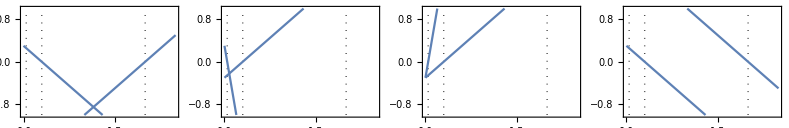

```mathematica
GraphicsRow[{
Plot[Subscript[Λ, 1]/.pars,{e,0,2.5},ImageSize->Small,Frame->True,Prolog->{Dotted,
Line[{{E1,-1},{E1,1}}],
Line[{{E2,-1},{E2,1}}],
Line[{{E3,-1},{E3,1}}]
},PlotRange->{-1,1}],
Plot[Subscript[Λ, 2]/.pars,{e,0,2.5},ImageSize->Small,Frame->True,Prolog->{Dotted,
Line[{{E1,-1},{E1,1}}],
Line[{{E2,-1},{E2,1}}],
Line[{{E3,-1},{E3,1}}]
},PlotRange->{-1,1}],
Plot[Subscript[Λ, 3]/.pars,{e,0,2.5},ImageSize->Small,Frame->True,Prolog->{Dotted,
Line[{{E1,-1},{E1,1}}],
Line[{{E2,-1},{E2,1}}],
Line[{{E3,-1},{E3,1}}]
},PlotRange->{-1,1}],
Plot[Subscript[Λ, 4]/.pars,{e,0,2.5},ImageSize->Small,Frame->True,Prolog->{Dotted,
Line[{{E1,-1},{E1,1}}],
Line[{{E2,-1},{E2,1}}],
Line[{{E3,-1},{E3,1}}]
},PlotRange->{-1,1}]
}]
```

From these plots, it follows that:

- Equilibrium 1 is stable between the second and third bifurcation point

- Equilibrium 2 is stable between the first and second bifurcation point

- Equilibrium 3 is stable before the first bifurcation point

- Equilibrium 4 is stable after the third bifurcation point

Now, we can piece together the bifurcation diagrams:

```mathematica
BifurcationDiagram[var_]:=Show[{
Plot[Evaluate[{var/.eql[[1]],var/.eql[[2]],var/.eql[[3]],var/.eql[[4]]}/.pars],{e,0,E1},PlotRange->{{0,2.5},{-0.05,1.05}},Frame->True,PlotStyle-> Tuples[{{Black},{Dashed,Dashed,,Dashed}}]],
Plot[Evaluate[{var/.eql[[1]],var/.eql[[2]],var/.eql[[3]],var/.eql[[4]]}/.pars],{e,E1,E2},PlotRange->{{0,2.5},{-0.05,1.05}},Frame->True,PlotStyle-> Tuples[{{Black},{Dashed,,Dashed,Dashed}}]],
Plot[Evaluate[{var/.eql[[1]],var/.eql[[2]],var/.eql[[3]],var/.eql[[4]]}/.pars],{e,E2,E3},PlotRange->{{0,2.5},{-0.05,1.05}},Frame->True,PlotStyle-> Tuples[{{Black},{,Dashed,Dashed,Dashed}}]],
Plot[Evaluate[{var/.eql[[1]],var/.eql[[2]],var/.eql[[3]],var/.eql[[4]]}/.pars],{e,E3,2.5},PlotRange->{{0,2.5},{-0.05,1.05}},Frame->True,PlotStyle->Tuples[{{Black},{Dashed,Dashed,Dashed,Black}}]]
}]
```

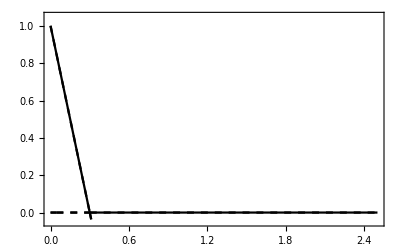

```mathematica
BifurcationDiagram[p[t]]
```

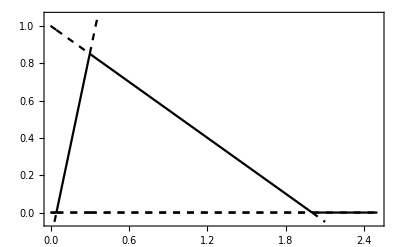

```mathematica
BifurcationDiagram[q[t]]
```

To summarise the qualitatively different outcomes of the model:

- in region I (e<0.045), only the superior competitor can exist in the metapopulation

- in region II (0.045<e<0.3), both species coexist in the metapopulation

- in region III (0.3<e<2.0), only the superior disperses can exist in the metapopulation

- in region IV (e>2), none of the species can exist in the metapopulation

Q(d): Consider also the parameter c_2 as a bifurcation parameter and attempt to plot boundary lines between qualitatively different parameter regimes in the 2D (e,c_2) parameter space

The earlier analysis indicated that the locations of the transcritical bifurcation points are given by:

```mathematica
T1=e/.bif1/.Subscript[c, 1]->0.3;
T2=e/.bif2/.Subscript[c, 1]->0.3;
T3=e/.bif3/.Subscript[c, 1]->0.3;
```

When we consider both e and c_2are allowed to vary as bifurcation parameters, the locations of the transcritical bifurcation points define three boundary lines between parameter regimes. When c_2 falls below the value of c_1, species 2 can never persist in the metapopulation with species 1: it always loses competition and it is also slower to disperse when c_2<c_1. Therefore, we find only two parameter regimes below  c_2=c_1.

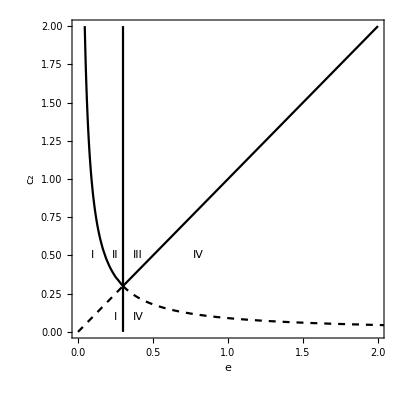

```mathematica
Show[{ContourPlot[{T1==e,T2==e,T3==e},{e,0,2.5},{Subscript[c, 2],0.3,2},PlotRange->{{0,2},{0,2}},ContourStyle->Black,FrameLabel->{e,Subscript[c, 2]},Epilog->{
Inset[Text["I"],{0.1,0.5}],
Inset[Text["II"],{0.25,0.5}],
Inset[Text["III"],{0.4,0.5}],
Inset[Text["IV"],{0.8,0.5}],
Inset[Text["IV"],{0.4,0.1}],
Inset[Text["I"],{0.25,0.1}]
}],
ContourPlot[{T1==e,T2==e,T3==e},{e,0,2.5},{Subscript[c, 2],0,0.3},PlotRange->{{0,2},{0,2}},ContourStyle->{{Dashed,Black}, Black,{Dashed,Black}}]
}]
```

## Ex. IV-2 Dynamics of a food chain

First, define the model equations and default parameters:

```mathematica
eqx=D[x[t],t]==r x[t](1-x[t]/K)-(Subscript[a, 1] x[t])/(1+Subscript[b, 1] x[t])y[t];
eqy=D[y[t],t]==Subscript[c, 1](Subscript[a, 1] x[t])/(1+Subscript[b, 1] x[t])y[t]-Subscript[d, 1] y[t]-(Subscript[a, 2] y[t])/(1+Subscript[b, 2] y[t])z[t];
eqz=D[z[t],t]==Subscript[c, 2](Subscript[a, 2] y[t])/(1+Subscript[b, 2] y[t])z[t]-Subscript[d, 2] z[t];
pars={r->1,K->1,Subscript[a, 1]->5,Subscript[a, 2]->0.1,Subscript[b, 2]->2.,Subscript[c, 1]->1,Subscript[c, 2]->1,Subscript[d, 1]->0.4,Subscript[d, 2]->0.01};
```

As we will be running lots of simulations for different values of the parameter b_1, it’s useful to write a procedure for running simulations first

```mathematica
simulate[b1_,initialPoint_List,T1_:500.0,T0_:0,showFinalState_:True]:=Module[{sys,sol,pl1,pl2},
sys=Join[Thread[{x[0],y[0],z[0]}==initialPoint],{eqx,eqy,eqz}/.pars/.{Subscript[b, 1]->b1}];
sol=NDSolve[sys,{x[t],y[t],z[t]},{t,0,T1}]//First;
If[showFinalState,Print["final state:  = ", {x[t],y[t],z[t]}/.sol/.t->T1]];
pl1=Plot[Evaluate[{x[t],y[t],z[t]}/.sol],{t,T0,T1},PlotStyle->{Darker[Green],Blue,Darker[Red]},Frame->True,FrameLabel->{t,"x,y,z"},AspectRatio->1];
pl2=ParametricPlot3D[{x[t],y[t],z[t]}/.sol,{t,T0,T1},AxesLabel->{x[t],y[t],z[t]},BoxRatios->{1,1,1},PlotStyle->Black,PlotRange->All];
GraphicsRow[{pl1,pl2},ImageSize->Large]
]
```

Q(b): Study the system numerically... Determine the eigenvalues of the Jacobian for the biologically interesting equilibrium point where all species are present.

Here is a simulation for the default parameter set and b_1=2.0. As you can see, the equilibrium is a stable spiral

final state:  = {0.750022,0.12499,13.75}

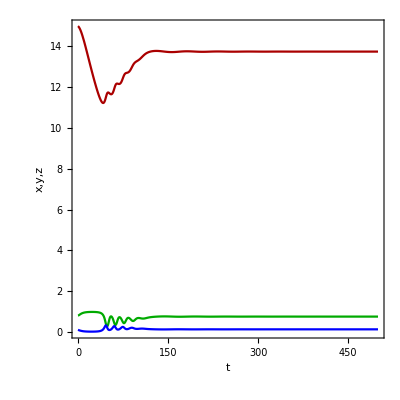

```mathematica
simulate[2.0,{0.8,0.1,15.0}]
```

The simulation result is confirmed by an analysis of the Jacobian at the equilibrium point

```mathematica
FindEigenvalues[b1_]:=Module[{eql,J},
eql=FindRoot[{eqx[[2]]==0,eqy[[2]]==0,eqz[[2]]==0}/.pars/.{Subscript[b, 1]->b1},{{x[t],0.75},{y[t],0.12},{z[t],13.75}}];
J=D[{eqx[[2]] , eqy[[2]] , eqz[[2]]}/.pars,{{x[t],y[t],z[t]}}]/.eql/.{Subscript[b, 1]->b1};
Eigenvalues[J]
]
```

There is one negative real eigenvalue and a complex conjugate eigenvalue pair with negative real parts

```mathematica
FindEigenvalues[2.0]
```

{-0.346628+0. ⅈ,-0.0166858+0.122287 ⅈ,-0.0166858-0.122287 ⅈ}

Q(d): Focus on the first bifurcation that occurs as b_1 is increased from 2 to 3, and verify that the equilibrium point changes stability. What kind of bifurcation occurs here?

The first bifurcation that occurs is a Hopf bifurcation. By plotting the eigenvalues of the Jacobian, you can see that it occurs at b_1≈2.135:

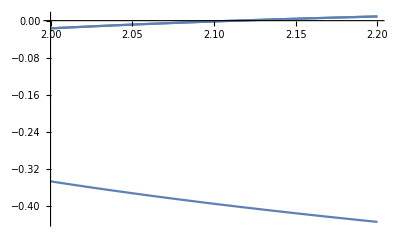

```mathematica
Plot[Re[FindEigenvalues[Subscript[b, 1]]],{Subscript[b, 1],2,2.2}]
```

Indeed, a simulation for b_1=2.15, just beyond the Hopf bifurcation point, shows that the food chain converges on a stable limit cycle

final state:  = {0.724024,0.144663,12.9584}

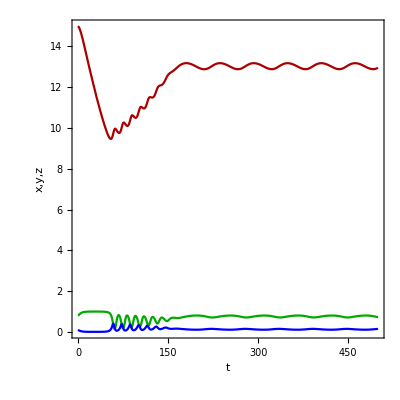

```mathematica
simulate[2.15, {0.8, 0.1, 15.0}]
```

To visualise the cycle better, we can only plot the final part of the simulation, after the system has converged on the attractor

final state:  = {0.777666,0.122001,12.8901}

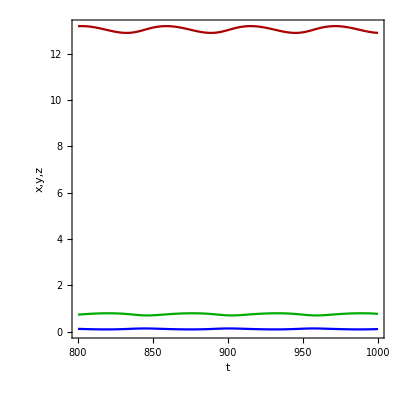

```mathematica
simulate[2.15, {0.75, 0.15, 13.0},1000,800]
```

Q(e): The second bifurcation is a bifurcation of a stable periodic orbit. What kind of bifurcation is it?

The second bifurcation occurs at b_1≈2.291. At this point the stable limit cycle undergoes a period-doubling bifurcation. The following plot show the cycle just before and after the bifurcation

final state:  = {0.833302,0.0949928,12.4365}

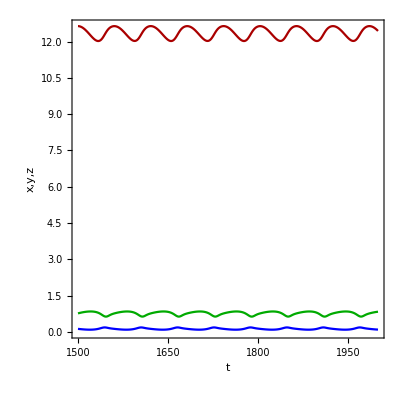

```mathematica
simulate[2.29, {0.75, 0.15, 13.0}, 2000, 1500]
```

final state:  = {0.680535,0.156354,12.5193}

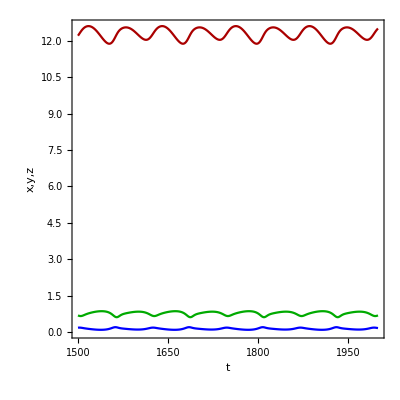

```mathematica
simulate[2.3, {0.75, 0.15, 13.0}, 2000, 1500]
```

Q(f): Describe the sequence of bifurcations that follow after the second bifurcation. What kind of attractor emerges as b_1approaches 3?

From the period-doubling bifurcation onwards, the attractor transforms through a complicated series of bifurcations. There are additional period-doubling bifurcations, until a homoclinic bifurcation of an unstable cycle gives rise to a first chaotic attractor. There are intermediate parameter regimes in which the dynamics appears to simplify again, but only temporarily: in the end, a complex chaotic attractor arises, producing irregular fluctuations of the three species.

The attractor after a second period-doubling bifurcation

final state:  = {0.823987,0.102238,12.0774}

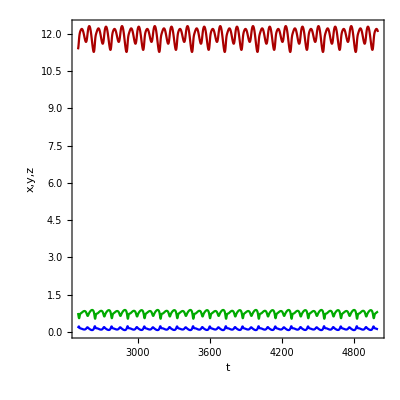

```mathematica
simulate[2.385, {0.75, 0.15, 13.0}, 5000, 2500]
```

```mathematica
Manipulate[simulate[Subscript[b, 1], {0.75, 0.15, 13.0}, 5000, 2500,False],{Subscript[b, 1],2,3}]
```

Q(g): Run two simulations of the three-species food chain for b_1=3, with slightly different initial conditions. Can you explain why this models is said to show sensitive dependence on initial conditions? What are the implications of this property for our ability to predict future species densities?

```mathematica
compareTwoSims[b1_,initialPoint_List,T_:500.0]:=Module[{sys1,sys2,sol1,sol2,pl1,pl2},
sys1=Join[Thread[{1.01x[0],y[0],z[0]}==initialPoint],{eqx,eqy,eqz}/.pars/.{Subscript[b, 1]->b1}];
sys2=Join[Thread[{0.99 x[0],y[0],z[0]}==initialPoint],{eqx,eqy,eqz}/.pars/.{Subscript[b, 1]->b1}];
sol1=NDSolve[sys1,{x[t],y[t],z[t]},{t,0,T}]//First;
sol2=NDSolve[sys2,{x[t],y[t],z[t]},{t,0,T}]//First;
pl1=Plot[Evaluate[{(x[t]/.sol1),(x[t]/.sol2)}],{t,0,T},PlotStyle->{Darker[Green],Darker[Red]},Frame->True,FrameLabel->{t,x[t]},AspectRatio->1];
pl2=Plot[(x[t]/.sol1)-(x[t]/.sol2),{t,0,T},PlotStyle->{Black},Frame->True,FrameLabel->{t,Δx[t]},AspectRatio->1,PlotRange->All];
GraphicsRow[{pl1,pl2},ImageSize->Large]
]
```

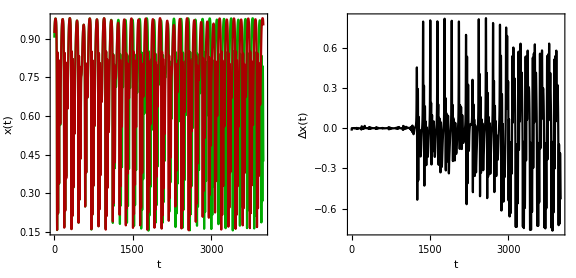

```mathematica
compareTwoSims[3.0,{0.9139010633373134,0.057542710868884746,10.17632631255382},4000]
```

Chaotic systems highlight a fundamental limitation to our ability to predict the future states of a dynamical system: in the long run, even small mistakes in measuring the initial conditions will tend to blow up to large discrepancies between the predicted and actual state. However, this model of a food chain illustrates that the prediction accuracy is often quite good if we do not attempt to predict too far ahead into the future.